# Pound-Drever-Hall Error Signal Derivation

## Derivation of PDH error signal, following March 18, 2026 tutorial here: https://ccahilla.github.io/lasers-and-optomechanics/tutorials/

#### 0. Fabry Perot cavity reflection as a function of phase

```mathematica
refl[ϕ_]:=(r1-r2 Exp[-I 2ϕ])/(1-r1 r2 Exp[-I 2ϕ]);
```

#### 1. What is the total electric field incident on the front of the cavity?

Carrier input

```mathematica
Ein=E0 Exp[I ω0 t];
```

Carrier + Upper Sideband + Lower Sideband

```mathematica
Eintotal=Ein(1+I Γ/2 Exp[I Ω t]+I Γ/2 Exp[-I Ω t])
```

ⅇ^(ⅈ t ω0) E0 (1+1/2 ⅈ ⅇ^(-ⅈ t Ω) Γ+1/2 ⅈ ⅇ^(ⅈ t Ω) Γ)

#### 2. Write down three single-pass phases ϕ0 , ϕusb , ϕlsb that the carrier, upper sideband, and lower sideband, will experience as they traverse the cavity, in terms of the cavity length L, and carrier and RF frequencies ω0 and Ω.

Where L is the nominal cavity length:

```mathematica
params={ϕ0->(ω0 L)/c,ϕusb->((ω0+Ω)L)/c,ϕlsb->((ω0-Ω)L)/c};
```

I have make this a list of parameters, so we can leave things in terms of ϕ0,ϕusb,ϕlsb,
Notice that we can also do another phase breakdown where 

ϕusb = ϕ0 + ϕrf and ϕlsb = ϕ0 - ϕrf
where
ϕrf = (Ω L)/c.

#### 3. Write down the cavity total reflected field Erefl in terms of the reflection function r(ϕ) and ϕ0 , ϕusb , ϕlsb

r0 is the reflected carrier refl[ϕ0],
rpΩ is the reflected upper sideband refl[ϕusb],
rmΩ is the reflected lower sideband refl[ϕlsb].

```mathematica
reflparams={r0->refl[ϕ0],rpΩ->refl[ϕusb],rmΩ->refl[ϕlsb]};
```

```mathematica
Erefltotal=Ein(r0+I Γ/2 rpΩ Exp[I Ω t]+I rmΩ Γ/2 Exp[-I Ω t]);
```

#### 4. Write down the cavity total reflected power P_refl (t) in terms of the reflection function r(ϕ) and ϕ0 , ϕusb , ϕlsb .

Use ComplexExpand, which assumes all variables are real variables, with Conjugate to quickly calculate our power.
However, in Mathematica we need to be careful because r0, rusb, and rlsb are NOT real variables, they are complex.
So when we take the complex conjugate we need to keep track of them.

I keep track of this manually below, by replacing r0, rusb, and rlsb with r0c, rusbc, and rlsbc, where the “c” suffix indicates complex conjugate.  
Not elegant but it works.

TrigToExp expands our trig expressions we get from FullSimplify into exponentials, which is easier to reach given our starting point

```mathematica
reflcparams={r0c->refl[-ϕ0],rpΩc->refl[-ϕusb],rmΩc->refl[-ϕlsb]};
```

```mathematica
Erefltotalc=TrigToExp[ComplexExpand[Conjugate[Erefltotal]]]/.{r0->r0c,rpΩ->rpΩc,rmΩ->rmΩc}
```

ⅇ^(-ⅈ t ω0) E0 r0c-1/2 ⅈ ⅇ^(ⅈ t Ω-ⅈ t ω0) E0 rmΩc Γ-1/2 ⅈ ⅇ^(-ⅈ t Ω-ⅈ t ω0) E0 rpΩc Γ

```mathematica
Prefltotal=TrigToExp[FullSimplify[ComplexExpand[Erefltotal Erefltotalc]]]
```

E0^2 r0 r0c+1/2 ⅈ ⅇ^(-ⅈ t Ω) E0^2 r0c rmΩ Γ-1/2 ⅈ ⅇ^(ⅈ t Ω) E0^2 r0 rmΩc Γ+1/2 ⅈ ⅇ^(ⅈ t Ω) E0^2 r0c rpΩ Γ-1/2 ⅈ ⅇ^(-ⅈ t Ω) E0^2 r0 rpΩc Γ+1/4 E0^2 rmΩ rmΩc Γ^2+1/4 ⅇ^(2 ⅈ t Ω) E0^2 rmΩc rpΩ Γ^2+1/4 ⅇ^(-2 ⅈ t Ω) E0^2 rmΩ rpΩc Γ^2+1/4 E0^2 rpΩ rpΩc Γ^2

```mathematica
Prefltotal=Prefltotal/.{Γ^2->0}
```

E0^2 r0 r0c+1/2 ⅈ ⅇ^(-ⅈ t Ω) E0^2 r0c rmΩ Γ-1/2 ⅈ ⅇ^(ⅈ t Ω) E0^2 r0 rmΩc Γ+1/2 ⅈ ⅇ^(ⅈ t Ω) E0^2 r0c rpΩ Γ-1/2 ⅈ ⅇ^(-ⅈ t Ω) E0^2 r0 rpΩc Γ

#### 5. Set the coefficient for e^(-i Ω t) equal to some complex number z, and the coefficient for e^(i Ω t) equal to y. What is z and y? Is there any connection between z and y? What is it?

First, Collect our P_refl(t) by using e^(-i Ω t) and e^(i Ω t) coefficients.

```mathematica
Collect[Prefltotal,{ⅇ^(ⅈ t Ω),ⅇ^(-ⅈ t Ω)}]
```

E0^2 r0 r0c+ⅇ^(ⅈ t Ω) (-1/2 ⅈ E0^2 r0 rmΩc Γ+1/2 ⅈ E0^2 r0c rpΩ Γ)+ⅇ^(-ⅈ t Ω) (1/2 ⅈ E0^2 r0c rmΩ Γ-1/2 ⅈ E0^2 r0 rpΩc Γ)

The first term above is the DC term, the second term associated with ⅇ^(ⅈ t Ω) is the y term, and the third term associated with ⅇ^(-ⅈ t Ω) is the z term:

```mathematica
z=Simplify[(1/2 ⅈ E0^2 r0c rmΩ Γ-1/2 ⅈ E0^2 r0 rpΩc Γ)]
y=Simplify[(-1/2 ⅈ E0^2 r0 rmΩc Γ+1/2 ⅈ E0^2 r0c rpΩ Γ)]
```

1/2 ⅈ E0^2 (r0c rmΩ-r0 rpΩc) Γ

-1/2 ⅈ E0^2 (r0 rmΩc-r0c rpΩ) Γ

Analyzing z and y we see that y is the complex conjugate of z.  
We can write y = z^*.

#### 6. Rewrite P_refl in terms of z and y.

Prefl=E0^2 r0 r0c+z^* ⅇ^(ⅈ t Ω) +z ⅇ^(-ⅈ t Ω)

#### 7. P_I + i P_Q = P^Ω . Show we can rewrite the demodulation in this way.

Cos[Ωt]+i Sin[Ωt] = e^(i Ω t), so we can combine our two real demodulations into a single complex demodulation.  This will gives us a complex number whose real and imaginary parts represent our usual I and Q outputs.

#### 8. Calculate the 1Ω demodulated power P_refl^Ω(ϕ0, ϕusb , ϕlsb). What can we see pops out?

Looking at our Prefl expression above:
Prefl=E0^2 r0 r0c+z^* ⅇ^(ⅈ t Ω) +z ⅇ^(-ⅈ t Ω) 
it’s clear that if we multiply by e^(i Ω t) and integrate Prefl by one cycle in Ωt, the DC term and ⅇ^(ⅈ t Ω) will go to ⅇ^(ⅈ t Ω) and ⅇ^(2ⅈ t Ω), and will integrate to zero over one cycle.

BUT the ⅇ^(-ⅈ t Ω) term goes to stationary in time, so we should get exactly z out of our demodulation:
P_refl^Ω = z.

```mathematica
PreflΩ=z
```

1/2 ⅈ E0^2 (r0c rmΩ-r0 rpΩc) Γ

#### 9. Calculate the derivative of P_refl^Ω with respect to ϕ0, then evaluate it about zero.

First, we must substitute all instances of ϕ0: ϕusb → ϕ0+ϕrf, ϕlsb → ϕ0 - ϕrf, as well as our reflection terms r(ϕ0).
Then we take the derivative, 
then evaluate at ϕ0 → 0.

```mathematica
dPreflΩdϕ0=Simplify[D[PreflΩ /. reflparams /. reflcparams /. {ϕusb->ϕ0+ϕrf,ϕlsb->ϕ0-ϕrf},ϕ0]];
```

```mathematica
dPreflΩdϕ0at0=Simplify[dPreflΩdϕ0/.{ϕ0->0}]
```

-(2 (-1+ⅇ^(2 ⅈ ϕrf)) E0^2 r1 (-1+r1^2) r2 (-1+ⅇ^(2 ⅈ ϕrf) r2^2) Γ)/((-1+r1 r2)^2 (-1+ⅇ^(2 ⅈ ϕrf) r1 r2)^2)

#### 10. Plot the real and imaginary parts of P_refl^Ω(ϕ_0, ϕusb, ϕlsb ) as a function of ϕ0 ∈ [−π, π].

Below we evaluate our (P^Ω)_refl signal.  
The main signal appears in the real quadrature, 
with some small blip in Q-quadrature due to a slight overlap in carrier and RF sideband resonances.
The discriminant (dP^Ω)_refl/dϕ_0×ϕ_0 is plotted as a dashed line, and gives our optical gain about resonance.

This error signal has a very distinctive shape, and is highly non-linear outside the region of carrier resonance.
But inside the resonance, it is very discriminating, and able to provide an excellent, strong, linear error signal.
This can be detected with a radio-frequency photodetector (RFPD). 

The RF sidebands do show up in our PDH error signal sweep, as the side lobes on either side of the carrier resonance.
The side lobes represent when the Upper Sideband or Lower Sideband starts to resonant inside the cavity.
The RF sidebands have a strong response in the imaginary quadrature, 
while the carrier does not.

```mathematica
values={L->1,T1->0.1,T2->0.1,r1->√(1-T1),r2->√(1-T2),
E0->1,Γ->0.1,ϕusb->ϕ0+ϕrf,ϕlsb->ϕ0-ϕrf,ϕrf->π/4};
```

```mathematica
PreflΩ/.reflparams/.reflcparams;
```

```mathematica
plotPreflΩ=PreflΩ/.reflparams/.reflcparams//.values;
```

```mathematica
plotdPreflΩdϕ0at0=dPreflΩdϕ0at0//.values;
```

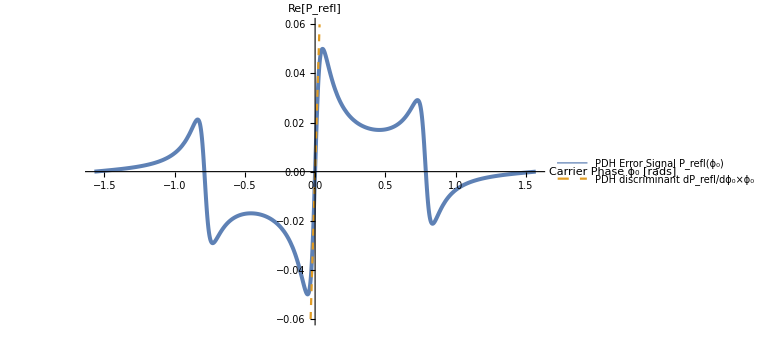

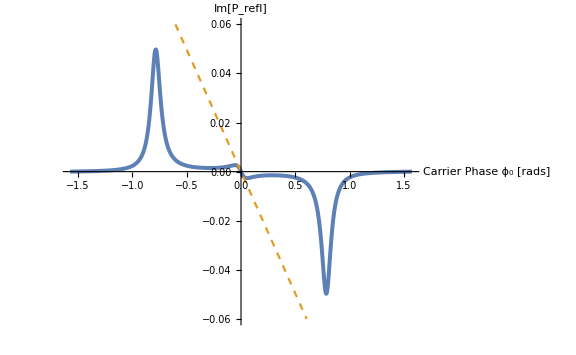

```mathematica
Plot[{Re[plotPreflΩ],Re[plotdPreflΩdϕ0at0 ϕ0]},{ϕ0,-π/2,π/2},PlotRange->{-0.06,0.06},PlotStyle->{Thickness[0.005],Dashed},PlotLegends->{"PDH Error Signal P_refl(ϕ_0)", "PDH discriminant dP_refl/dϕ_0×ϕ_0"},AxesLabel->{"Carrier\nPhase ϕ_0\n[rads]","Re[P_refl]"},ImageSize->Large]
Plot[{Im[plotPreflΩ],Im[plotdPreflΩdϕ0at0 ϕ0]},{ϕ0,-π/2,π/2},PlotRange->{-0.06,0.06},PlotStyle->{Thickness[0.005],Dashed},AxesLabel->{"Carrier\nPhase ϕ_0\n[rads]","Im[P_refl]"},ImageSize->Large]
```

#### Manipulate plot of PDH error signal P_refl/Γ(ϕ0,ϕrf)

For fun, in the manipulate plot, I’ve added in the Demod Angle ζ, which is just a simple rotation of the detected I and Q quadrature.
The way to consider the demod phase is similar to the arbitrary phase accrued while transmitting to the photodetector.
We can explicitly consider it while demodulating by demodulating over Cos[Ωt+ζ] and Sin[Ωt+ζ].  
If we set ζ = π/2, we’ll flip which quadrature our signal is in.

```mathematica
manivalues2={L->1,r1->√(1-T1),r2->√(1-T2),E0->1,ϕusb->ϕ0+ϕrf,ϕlsb->ϕ0-ϕrf}
```

{L→1,r1→√(1-T1),r2→√(1-T2),E0→1,ϕusb→ϕ0+ϕrf,ϕlsb→ϕ0-ϕrf}

```mathematica
maniPreflΩ[ϕ0_,ϕrf_,Γ_,T1_,T2_]:=Evaluate[PreflΩ/.reflparams/.reflcparams//.manivalues2]
```

```mathematica
Manipulate[
Column[{
Plot[Re[maniPreflΩ[ϕ0,ϕrf,Γ,T1,T2]Exp[I ζ]],{ϕ0,-π/2,π/2},PlotRange->Full,PlotLegends->{"PDH Error Signal P_refl(ϕ_0)", "PDH discriminant dP_refl/dϕ_0×ϕ_0"},AxesLabel->{"Carrier\nPhase ϕ_0\n[rads]","Re[(P^Ω)_refl]"},ImageSize->Large,PlotPoints->200],
Plot[Im[maniPreflΩ[ϕ0,ϕrf,Γ,T1,T2]Exp[I ζ]],{ϕ0,-π/2,π/2},PlotRange->Full,AxesLabel->{"Carrier\nPhase ϕ_0\n[rads]","Im[(P^Ω)_refl]"},ImageSize->Large,PlotPoints->200]
}],
{{ϕrf,π/4,"RF Phase ϕrf [rads]"},0,π/2},
{{Γ,0.1,"RF Modulation Depth Γ [rads]"},0,0.5},
{{T1,0.1,"Input Mirror Transmission T_1"},0,1},
{{T2,0.1,"End Mirror Transmission T_2"},0,1},
{{ζ,0,"Demod Angle ζ [rads]"},-π,π},
Paneled->False
]
```

#### 11. Plot P_refl^Ω as a phasor as a function of φ0 ∈ [− π/2,π/2]

Below we evaluate our (P^Ω)_refl signal as a phasor.
The carrier resonance is the line almost perfectly along the real axis.
The circles are the RF sideband sidelobes.

Those circles are representative of the reflection of the RF sidebands off the cavity, rotated by either + or -90°.  
If we increase the cavity finesse by lowering the mirror transmission T2 or T1, our signals get stronger and cleaner,
as the improved finesse of the cavity shrinks the size of the resonance, preventing mixing.

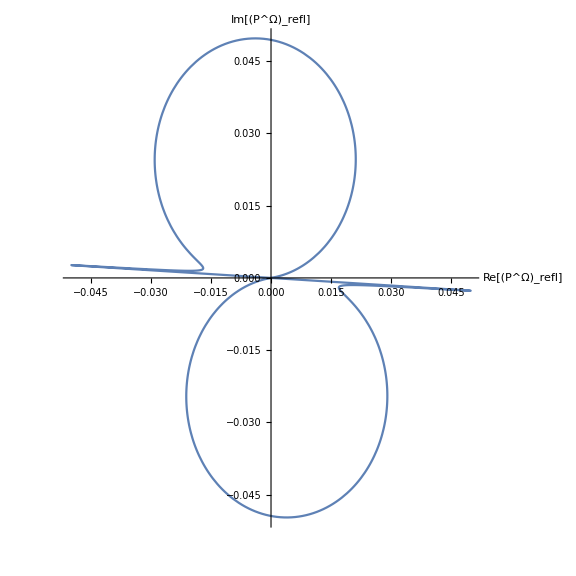

```mathematica
ParametricPlot[{Re[plotPreflΩ],Im[plotPreflΩ]},{ϕ0,-π/2,π/2},AspectRatio->1,PlotRange->Full,AxesLabel->{"Re[(P^Ω)_refl]","Im[(P^Ω)_refl]"},ImageSize->Large]
```

#### Manipulate plot of PDH phasor

```mathematica
Manipulate[
ParametricPlot[{Re[maniPreflΩ[ϕ0,ϕrf,Γ,T1,T2]Exp[I ζ]],Im[maniPreflΩ[ϕ0,ϕrf,Γ,T1,T2]Exp[I ζ]]},{ϕ0,-π/2,π/2},PlotRange->Full,PlotLegends->{"PDH Error Signal P_refl(ϕ_0)"},AxesLabel->{"Re[(P^Ω)_refl]","Im[(P^Ω)_refl]"},ImageSize->Large,PlotPoints->200],
{{ϕrf,π/4,"RF Phase ϕrf [rads]"},0,π/2},
{{Γ,0.1,"RF Modulation Depth Γ [rads]"},0,0.5},
{{T1,0.1,"Input Mirror Transmission T_1"},0,1},
{{T2,0.1,"End Mirror Transmission T_2"},0,1},
{{ζ,0,"Demod Angle ζ [rads]"},-π,π},
Paneled->False
]
```